# Analysis of Antigen output

## Basic parameters

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetDirectory["../"];
```

```mathematica
Quiet[CreateDirectory["figures/"]];
```

### Type colors

```mathematica
yC=RGBColor[0.893,0.385,0.248];
```

```mathematica
vC=RGBColor[0.894,0.664,0.303];
```

```mathematica
bC=Blend[{yC,vC}];
```

```mathematica
h1C=RGBColor[0.323,0.34,0.805];
```

```mathematica
h3C=RGBColor[0.374,0.625,0.766];
```

```mathematica
typeColors={h3C,h1C,vC,yC};
```

```mathematica
typeColorRules=MapThread[#1->#2&,{{"H3N2","H1N1","Vic","Yam"},typeColors}];
```

## Loess fit

```mathematica
LoessFit[(x_)?VectorQ,data_,α_:0.75,λ_:1]:=Table[LoessFit[x[[i]],data,α,λ],{i,Length[x]}]
```

```mathematica
LoessFit[(x_)?NumberQ,data_,α_:0.75,λ_:1]:=WLSFit[data,LoessWts[x,data,α],λ,x];
```

```mathematica
WLSFit[data_,wts_,ldegree_:1,x_]:=Fit[Transpose[(wts*#1&)/@Join[{Table[1,{Length[data]}]},Transpose[data]]],Join[{u},Table[v^i,{i,ldegree}]],{u,v}]/.{u->1,v->x}
```

```mathematica
LoessWts[x_,data_,α_]:=Tricube[(x-First[Transpose[data]])/LoessDistance[x,data,α]]
```

```mathematica
Tricube=Compile[{{x,_Real,1}},If[Abs[#]<1,(1-Abs[#]^3)^3,0]&/@x];
```

```mathematica
LoessDistance[x_,data_,α_]:=Module[{A=Max[1,α],X=First[Transpose[data]],q},q=Min[Length[X],Ceiling[α*Length[X]]];A*Sort[Abs[X-x]][[q]]]
```

## Options

```mathematica
fontSize=10;
```

```mathematica
imageSize=300;
```

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListContourPlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize];
```

```mathematica
SetOptions[ContourPlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize];
```

```mathematica
SetOptions[DiscretePlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->imageSize,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->imageSize,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Histogram,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All},ChartStyle->EdgeForm[Thin]];
```

```mathematica
SetOptions[SmoothDensityHistogram,FrameStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

## Summary

### Indices

```mathematica
indexRules=MapIndexed[#1->#2[[1]]&,{"mig","inc","drift","div","childPro","persistence"}]
```

{mig→1,inc→2,drift→3,div→4,childPro→5,persistence→6}

```mathematica
nameRules=MapThread[#1->#2&,{{"mig","inc","drift","div","childPro","persistence"},{"migration rate","incidence","antigenic drift","diversity","childhood infections","persistence"}}]
```

{mig→migration rate,inc→incidence,drift→antigenic drift,div→diversity,childPro→childhood infections,persistence→persistence}

```mathematica
nameRules=MapThread[#1->#2&,{{"mig","inc","drift","div","childPro","persistence"},{"migration rate","attack rate","antigenic drift","diversity","childhood infections","persistence"}}]
```

{mig→migration rate,inc→attack rate,drift→antigenic drift,div→diversity,childPro→childhood infections,persistence→persistence}

### Data

```mathematica
mutationRates={"0.00005","0.00015","0.00025","0.00035","0.00045","0.00055","0.00065"};
```

```mathematica
mixingCategories={"eq","diff"};
```

```mathematica
replicates={"1","2","3","4","5","6","7","8"};
```

```mathematica
getStatistic[mutationRate_,mixingCategory_,statistic_,replicate_]:=Module[{stem},
stem="replicate_"<>replicate<>"/antigen_mu_"<>mutationRate<>"_"<>mixingCategory<>"_"<>replicate<>"/out.stats";
If[FileExistsQ[stem],Import[stem,"Table"][[2,statistic/.indexRules]],Null]
]
```

```mathematica
getStatistic[mutationRate_,mixingCategory_,statistic_]:=Module[{statistics},
statistics=Map[getStatistic[mutationRate,mixingCategory,statistic,#]&,replicates];
statistics=DeleteCases[statistics,Null];
If[Length[statistics]>0,Mean[statistics],Null]
]
```

```mathematica
getStatistic["0.00005","diff","mig"]
```

0.468625

```mathematica
getStatisticSE[mutationRate_,mixingCategory_,statistic_]:=Module[{statistics},
statistics=Map[getStatistic[mutationRate,mixingCategory,statistic,#]&,replicates];
statistics=DeleteCases[statistics,Null];
If[Length[statistics]>1,StandardDeviation[statistics],Null]
]
```

```mathematica
getStatisticLower[mutationRate_,mixingCategory_,statistic_]:=Module[{mean,se},
mean=getStatistic[mutationRate,mixingCategory,statistic];
se=getStatisticSE[mutationRate,mixingCategory,statistic];
If[NumberQ[se],mean-se,Null]
]
```

```mathematica
getStatisticLower[mutationRate_,mixingCategory_,statistic_]:=Module[{statistics},
statistics=Map[getStatistic[mutationRate,mixingCategory,statistic,#]&,replicates];
statistics=DeleteCases[statistics,Null];
If[Length[statistics]>1,Min[statistics],Null]
]
```

```mathematica
getStatisticLower["0.00005","eq","mig"]
```

0.473

```mathematica
getStatisticUpper[mutationRate_,mixingCategory_,statistic_]:=Module[{mean,se},
mean=getStatistic[mutationRate,mixingCategory,statistic];
se=getStatisticSE[mutationRate,mixingCategory,statistic];
If[NumberQ[se],mean+se,Null]
]
```

```mathematica
getStatisticUpper[mutationRate_,mixingCategory_,statistic_]:=Module[{statistics},
statistics=Map[getStatistic[mutationRate,mixingCategory,statistic,#]&,replicates];
statistics=DeleteCases[statistics,Null];
If[Length[statistics]>1,Max[statistics],Null]
]
```

```mathematica
getStatisticUpper["0.00005","diff","mig"]
```

0.574

## Line plot

```mathematica
red=ColorData["Rainbow"][0.95];
```

```mathematica
linePlot[statistic_]:=Module[{eqPairs,diffPairs,lines,points},
eqPairs=DeleteCases[Table[{ToExpression[m],getStatistic[m,"eq",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
diffPairs=DeleteCases[Table[{ToExpression[m],getStatistic[m,"diff",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
lines=ListLinePlot[{eqPairs,diffPairs},PlotRange->All,PlotRangePadding->Scaled[0.05],PlotStyle->{Gray,Lighter[red,0.1]},ImageSize->200,FrameTicks->{{Automatic,None},{Table[{i,i*10000,{0,0.005}},{i,0,0.0006,0.0001}],None}},FrameLabel->{"antigenic mutation rate (× 10^-4)",statistic/.nameRules}];
points=ListPlot[{eqPairs,diffPairs},PlotStyle->{GrayLevel[0.25],Darker[red,0.1]}];
Show[lines,points]
]
```

```mathematica
linePlot[statistic_]:=Module[{adj,eqMeans,eqLower,eqUpper,diffMeans,diffLower,diffUpper,lines,intervals,points},
adj=0;
eqMeans=DeleteCases[Table[{ToExpression[m]-adj,getStatistic[m,"eq",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
eqLower=DeleteCases[Table[{ToExpression[m]-adj,getStatisticLower[m,"eq",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
eqUpper=DeleteCases[Table[{ToExpression[m]-adj,getStatisticUpper[m,"eq",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
diffMeans=DeleteCases[Table[{ToExpression[m]+adj,getStatistic[m,"diff",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
diffLower=DeleteCases[Table[{ToExpression[m]+adj,getStatisticLower[m,"diff",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
diffUpper=DeleteCases[Table[{ToExpression[m]+adj,getStatisticUpper[m,"diff",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
lines=ListLinePlot[{eqMeans,diffMeans},PlotRange->All,PlotRangePadding->Scaled[0.05],PlotStyle->{Gray,Lighter[red,0.1]},ImageSize->200,FrameTicks->{{Automatic,None},{Table[{i,i*10000,{0,0.005}},{i,0,0.0006,0.0001}],None}},FrameLabel->{"antigenic mutation rate (× 10^-4)",statistic/.nameRules}];
intervals=ListPlot[{eqLower,eqUpper,diffLower,diffUpper},PlotStyle->None,Filling->{1->{{2},Gray},3->{{4},Lighter[red,0.1]}},FillingStyle->Gray];
points=ListPlot[{eqMeans,diffMeans},PlotStyle->{GrayLevel[0.25],Darker[red,0.1]}];
Show[lines,intervals,points]
]
```

```mathematica
linePlot[statistic_]:=Module[{ymax,eqCol,diffCol,adj,eqMeans,eqLower,eqUpper,diffMeans,diffLower,diffUpper,lines,bands,intervals,points,labels},
eqCol=GrayLevel[0.4];
diffCol=GrayLevel[0.1];
adj=0.000005;
adj=0;
eqMeans=DeleteCases[Table[{ToExpression[m]-adj,getStatistic[m,"eq",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
eqLower=DeleteCases[Table[{ToExpression[m]-adj,getStatisticLower[m,"eq",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
eqUpper=DeleteCases[Table[{ToExpression[m]-adj,getStatisticUpper[m,"eq",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
diffMeans=DeleteCases[Table[{ToExpression[m]+adj,getStatistic[m,"diff",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
diffLower=DeleteCases[Table[{ToExpression[m]+adj,getStatisticLower[m,"diff",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
diffUpper=DeleteCases[Table[{ToExpression[m]+adj,getStatisticUpper[m,"diff",statistic]},{m,mutationRates}],x_/;x[[2]]==Null];
ymax=Max[eqUpper[[All,2]],diffUpper[[All,2]]];
lines=ListLinePlot[{eqMeans,diffMeans},PlotRange->{Automatic,ymax},PlotRangePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.05],Scaled[0.05]}},PlotStyle->{eqCol,Directive[diffCol,Dashed]},ImageSize->200,FrameTicks->{{Automatic,None},{Table[{i,i*10000,{0,0.005}},{i,0,0.0006,0.0001}],None}},FrameLabel->{"antigenic mutation rate (× 10^-4)",statistic/.nameRules}];
bands=ListLinePlot[{{{0.00012,10},{0.00018,10}},{{0.00027,10},{0.00033,10}},{{0.00052,10},{0.00058,10}}},ImageSize->200,Filling->Axis,PlotStyle->{bC,h1C,h3C}];
intervals=ListPlot[{eqLower,eqUpper,diffLower,diffUpper},PlotStyle->None,Filling->{1->{{2},eqCol},3->{{4},diffCol}}];
points=ListPlot[{eqMeans,diffMeans},PlotStyle->{eqCol,diffCol}];
labels=Graphics[{Style[Text["H3",{0.00055,ymax},{0,0}],FontFamily->"Helvetica",Darker[h3C,0.5],FontSize->9],Style[Text["H1",{0.0003,ymax},{0,0}],FontFamily->"Helvetica",Darker[h1C,0.5],FontSize->9],Style[Text["B",{0.00015,ymax},{0,0}],FontFamily->"Helvetica",Darker[bC,0.5],FontSize->9]}];
Show[lines,bands,intervals,points,labels,ImageSize->200]
]
```

```mathematica
plots=Map[linePlot,{"inc","drift","childPro","mig"}];
```

```mathematica
fig=Grid[Partition[plots,2],Spacings->{0.75,1}];
```

## Scatterplot

```mathematica
loessAlpha=0.6;
```

### Scatterplot

```mathematica
scatterPlot[statistic_,min_,max_,ticksStep_,label_]:=Module[{eqPairs,diffPairs,eqLine,diffLine,ticks,bands,labels,pointPlot,linePlot},
eqPairs=DeleteCases[Flatten[Table[{getStatistic[m,"eq","drift",r],getStatistic[m,"eq",statistic,r]},{m,mutationRates},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null||x[[1]]>1.3];
diffPairs=DeleteCases[Flatten[Table[{getStatistic[m,"diff","drift",r],getStatistic[m,"diff",statistic,r]},{m,mutationRates},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null||x[[1]]>1.3];
eqLine=Table[{x,LoessFit[x,eqPairs,loessAlpha]},{x,0,2,0.1}];
diffLine=Table[{x,LoessFit[x,diffPairs,loessAlpha]},{x,0,2,0.1}];
ticks={{Table[{i,i,{0,0.01}},{i,0,max,ticksStep}],None},{Table[{i,i,{0,0.01}},{i,0,1.5,0.3}],None}};
eqPairs=Cases[eqPairs,x_/;x[[2]]>min];
diffPairs=Cases[diffPairs,x_/;x[[2]]>min];
pointPlot=ListPlot[{eqPairs,diffPairs},AspectRatio->0.6,ImagePadding->{{40,5},{35,10}},PlotStyle->{GrayLevel[0.25],Darker[red,0.1]},PlotRangePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.05],Scaled[0.1]}},PlotTheme->"FullAxes",PlotRange->{{0,All},{min,max}},PlotRangeClipping->False,ImageSize->200,FrameLabel->{"antigenic drift",statistic/.nameRules},FrameTicks->ticks];
linePlot=ListLinePlot[{eqLine,diffLine},PlotStyle->{GrayLevel[0.25],Darker[red,0.1]}];
bands=ListLinePlot[{{{0.1,max},{0.3,max}},{{0.5,max},{0.7,max}},{{1.0,max},{1.2,max}}},Filling->min,PlotStyle->None,FillingStyle->Opacity[0.1]];
labels=Graphics[{Style[Text["H3",{1.1,max},{0,-1}],FontFamily->"Helvetica",GrayLevel[0.2],FontSize->9],Style[Text["H1",{0.6,max},{0,-1}],FontFamily->"Helvetica",GrayLevel[0.2],FontSize->9],Style[Text["B",{0.2,max},{0,-1}],FontFamily->"Helvetica",GrayLevel[0.2],FontSize->9],Style[Text[ToString[label],Scaled[{-0.05,1.0}],{0,1}],FontFamily->"Helvetica",Bold,GrayLevel[0.2],FontSize->11]}];
Show[pointPlot,bands,linePlot,labels]
]
```

```mathematica
scatterPlotVsMu[statistic_,min_,max_,ticksStep_,label_]:=Module[{eqPairs,diffPairs,eqLine,diffLine,ticks,bands,labels,pointPlot,linePlot},
eqPairs=DeleteCases[Flatten[Table[{ToExpression[m]*1000,getStatistic[m,"eq",statistic,r]},{m,mutationRates},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null];
diffPairs=DeleteCases[Flatten[Table[{ToExpression[m]*1000,getStatistic[m,"diff",statistic,r]},{m,mutationRates},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null];
eqLine=Table[{x,LoessFit[x,eqPairs,loessAlpha]},{x,0.03,1,0.05}];
diffLine=Table[{x,LoessFit[x,diffPairs,loessAlpha]},{x,0.03,1,0.05}];
ticks={{Table[{i,i,{0,0.01}},{i,0,max,ticksStep}],None},{Table[{i,i,{0,0.01}},{i,0,1,0.2}],None}};
eqPairs=Cases[eqPairs,x_/;x[[2]]>min];
diffPairs=Cases[diffPairs,x_/;x[[2]]>min];
pointPlot=ListPlot[{eqPairs,diffPairs},ImagePadding->{{40,5},{35,10}},AspectRatio->0.6,PlotStyle->{GrayLevel[0.25],Darker[red,0.1]},PlotRangePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.05],Scaled[0.1]}},PlotTheme->"FullAxes",PlotRange->{All,{min,max}},PlotRangeClipping->False,ImageSize->200,FrameLabel->{"antigenic mutation rate (10^-3)",statistic/.nameRules},FrameTicks->ticks];
linePlot=ListLinePlot[{eqLine,diffLine},PlotStyle->{GrayLevel[0.25],Darker[red,0.1]}];
labels=Graphics[{Style[Text[ToString[label],Scaled[{-0.05,1.0}],{0,1}],FontFamily->"Helvetica",Bold,GrayLevel[0.2],FontSize->11]}];
Show[pointPlot,linePlot,labels]
]
```

```mathematica
rSquareds[statistic_]:=Module[{eqPairs,diffPairs,eqMean,eqSqResiduals,eqSqTotals,eqRSquared,diffMean,diffSqResiduals,diffSqTotals,diffRSquared},
eqPairs=DeleteCases[Flatten[Table[{getStatistic[m,"eq","drift",r],getStatistic[m,"eq",statistic,r]},{m,mutationRates},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null];
diffPairs=DeleteCases[Flatten[Table[{getStatistic[m,"diff","drift",r],getStatistic[m,"diff",statistic,r]},{m,mutationRates},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null];
eqMean=Mean[eqPairs[[All,2]]];
eqSqResiduals=Total[MapThread[(#2-LoessFit[#1,eqPairs,0.3])^2&,{eqPairs[[All,1]],eqPairs[[All,2]]}]];
eqSqTotals=Total[Map[(#-eqMean)^2&,eqPairs[[All,2]]]];
eqRSquared=1-eqSqResiduals/eqSqTotals;
diffMean=Mean[diffPairs[[All,2]]];
diffSqResiduals=Total[MapThread[(#2-LoessFit[#1,diffPairs,0.3])^2&,{diffPairs[[All,1]],diffPairs[[All,2]]}]];
diffSqTotals=Total[Map[(#-diffMean)^2&,diffPairs[[All,2]]]];
diffRSquared=1-diffSqResiduals/diffSqTotals;
{eqRSquared,diffRSquared}
]
```

```mathematica
rs=Map[#->rSquareds[#]&,{"inc","childPro","mig"}]
```

{inc→{0.975952,0.951427},childPro→{0.864876,0.895266},mig→{0.885384,0.907581}}

```mathematica
plots={scatterPlotVsMu["drift",0,1.55,0.4,"a"],scatterPlot["inc",0.008,0.07,0.02,"b"],scatterPlot["childPro",0.4,0.74,0.1,"c"],scatterPlot["mig",0.46,0.88,0.1,"d"]};
```

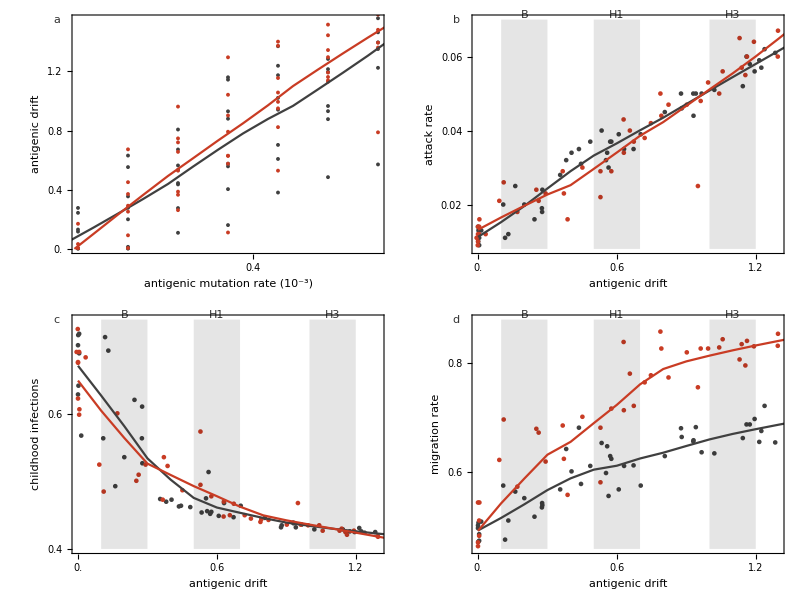

```mathematica
fig=Grid[Partition[plots,2],Spacings->{1,1}]
```

```mathematica
Export["figures/model_results.png",fig,"PNG",ImageResolution->300]
```

figures/model_results.png

```mathematica
Export["figures/model_results.pdf",fig,"PDF"]
```

figures/model_results.pdf

## Persistence

```mathematica
loessAlpha=0.6;
```

```mathematica
mutationRates={"0.00005","0.00015","0.00025","0.00035","0.00045","0.00055","0.00065"};
```

```mathematica
episilons={"0.00","0.04","0.08","0.12"};
```

```mathematica
replicates={"1","2","3","4","5","6","7","8"};
```

```mathematica
getStatistic[mutationRate_,mixingCategory_,statistic_,replicate_]:=Module[{stem},
stem="persistence_"<>replicate<>"/antigen_mu_"<>mutationRate<>"_"<>mixingCategory<>"/out.stats";
If[FileExistsQ[stem],Import[stem,"Table"][[2,statistic/.indexRules]],Null]
]
```

```mathematica
scatterPlot[statistic_,min_,max_,ticksStep_,eps_,label_,panelLabel_]:=Module[{pairs,tpairs,lm,slope,pvalue,line,ticks,bands,labels,pointPlot,linePlot},
pairs=DeleteCases[Flatten[Table[{getStatistic[m,"eps_"<>ToString[eps],"drift",r],getStatistic[m,"eps_"<>ToString[eps],statistic,r]},{m,mutationRates},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null||x[[1]]>1.3];
lm=LinearModelFit[pairs,{1,x},x];
slope=lm[1]-lm[0];
pvalue=lm["ParameterPValues"][[2]];
line=Table[{x,lm[x]},{x,0,2,0.1}];
ticks={{Table[{i,i,{0,0.01}},{i,0,max,ticksStep}],None},{Table[{i,i,{0,0.01}},{i,0,1.5,0.3}],None}};
pairs=Cases[pairs,x_/;x[[2]]>min];
pointPlot=ListPlot[pairs,AspectRatio->0.65,PlotStyle->GrayLevel[0.35],PlotRangePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.05],Scaled[0.1]}},PlotTheme->"FullAxes",PlotRange->{{0,All},{min,max}},PlotRangeClipping->False,ImagePadding->{{40,5},{32,10}},ImageSize->200,FrameLabel->{"antigenic drift",statistic/.nameRules},FrameTicks->ticks];
linePlot=ListLinePlot[line,PlotStyle->GrayLevel[0.2]];
bands=ListLinePlot[{{{0.1,max},{0.3,max}},{{0.5,max},{0.7,max}},{{1.0,max},{1.2,max}}},Filling->min,PlotStyle->None,FillingStyle->Opacity[0.1]];
labels=Graphics[{Style[Text["H3",{1.1,max},{0,-1}],FontFamily->"Helvetica",GrayLevel[0.2],FontSize->9],Style[Text["H1",{0.6,max},{0,-1}],FontFamily->"Helvetica",GrayLevel[0.2],FontSize->9],Style[Text["B",{0.2,max},{0,-1}],FontFamily->"Helvetica",GrayLevel[0.2],FontSize->9],Style[Text[label,Scaled[{0.01,1.0}],{-1,-1}],FontFamily->"Helvetica",Bold,GrayLevel[0.2],FontSize->10],Style[Text[panelLabel,Scaled[{-0.2,1.0}],{-1,0}],FontFamily->"Helvetica",Bold,GrayLevel[0.2],FontSize->13]}];
Show[pointPlot,bands,linePlot,labels]
]
```

```mathematica
linearFit[statistic_,eps_]:=Module[{pairs,lm,slope,pvalue},
pairs=DeleteCases[Flatten[Table[{getStatistic[m,"eps_"<>ToString[eps],"drift",r],getStatistic[m,"eps_"<>ToString[eps],statistic,r]},{m,mutationRates},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null||x[[1]]>1.3];
lm=LinearModelFit[pairs,{1,x},x];
slope=lm[1]-lm[0];
pvalue=lm["ParameterPValues"][[2]];
lm["ParameterTable"]
]
```

```mathematica
Map[linearFit["persistence",#]&,{"0.00","0.04","0.08","0.12"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 2.426 | 0.249526 | 9.72242 | 2.58239×10^-12
x | -1.20668 | 0.297535 | -4.0556 | 0.000212196, | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.79915 | 0.118254 | 15.2143 | 2.96984×10^-17
x | -0.707117 | 0.156336 | -4.52305 | 0.0000638735, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.934247 | 0.0763878 | 12.2303 | 6.37933×10^-15
x | -0.0670149 | 0.102702 | -0.652518 | 0.517895, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.685624 | 0.0388767 | 17.6359 | 9.45784×10^-21
x | -0.13496 | 0.0521346 | -2.58868 | 0.0132716}

```mathematica
plots=MapThread[scatterPlot["persistence",0,3.2,1,#1,#2,#3]&,{{"0.00","0.04","0.08","0.12"},{"ϵ = 0.00","ϵ = 0.04","ϵ = 0.08","ϵ = 0.12"},{"a","","",""}}];
```

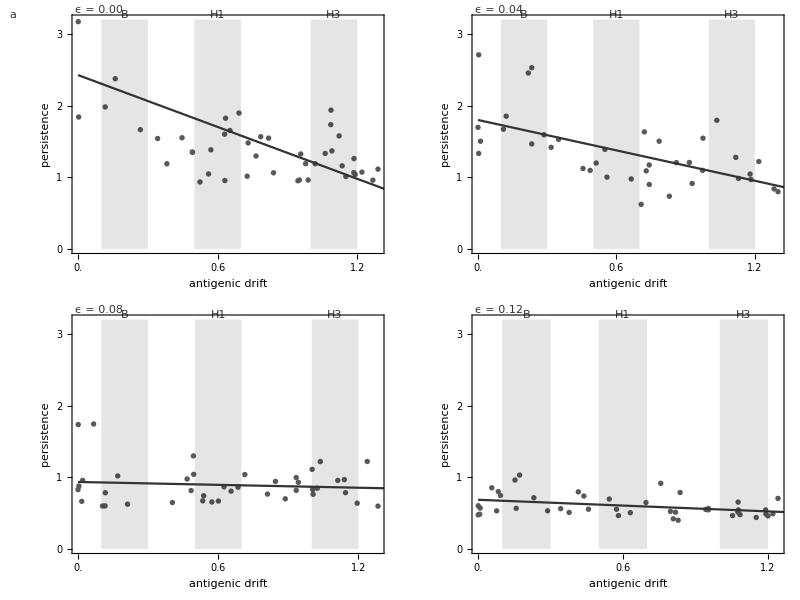

```mathematica
persistenceFig=Grid[Partition[plots,2],Spacings->{1,1}]
```

```mathematica
Export["figures/model_persistence.png",persistenceFig,"PNG",ImageResolution->300]
```

figures/model_persistence.png

```mathematica
Export["figures/model_persistence.pdf",persistenceFig,"PDF"]
```

figures/model_persistence.pdf

## Scatterplot across beta

```mathematica
loessAlpha=0.6;
```

```mathematica
betas={"0.70","0.75","0.79","0.84","0.88","0.92","0.97","1.06"};
```

```mathematica
mixingCategories={"eq","diff"};
```

```mathematica
replicates={"1","2","3","4","5","6","7","8"};
```

```mathematica
getStatistic[mutationRate_,mixingCategory_,statistic_,replicate_]:=Module[{stem},
stem="transmission_"<>replicate<>"/antigen_beta_"<>mutationRate<>"_"<>mixingCategory<>"/out.stats";
If[FileExistsQ[stem],Import[stem,"Table"][[2,statistic/.indexRules]],Null]
]
```

```mathematica
scatterPlot[statistic_,min_,max_,ticksStep_,label_]:=Module[{eqPairs,diffPairs,eqLine,diffLine,ticks,bands,labels,pointPlot,linePlot},
eqPairs=DeleteCases[Flatten[Table[{getStatistic[beta,"eq","drift",r],getStatistic[beta,"eq",statistic,r]},{beta,betas},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null||x[[1]]>1.3];
diffPairs=DeleteCases[Flatten[Table[{getStatistic[beta,"diff","drift",r],getStatistic[beta,"diff",statistic,r]},{beta,betas},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null||x[[1]]>1.3];
eqLine=Table[{x,LoessFit[x,eqPairs,loessAlpha]},{x,0,2,0.1}];
diffLine=Table[{x,LoessFit[x,diffPairs,loessAlpha]},{x,0,2,0.1}];
ticks={{Table[{i,i,{0,0.01}},{i,0,max,ticksStep}],None},{Table[{i,i,{0,0.01}},{i,0,1.5,0.3}],None}};
eqPairs=Cases[eqPairs,x_/;x[[2]]>min];
diffPairs=Cases[diffPairs,x_/;x[[2]]>min];
pointPlot=ListPlot[{eqPairs,diffPairs},AspectRatio->0.6,ImagePadding->{{40,5},{32,10}},PlotStyle->{GrayLevel[0.25],Darker[red,0.1]},PlotRangePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.05],Scaled[0.1]}},PlotTheme->"FullAxes",PlotRange->{{0,All},{min,max}},PlotRangeClipping->True,ImageSize->200,FrameLabel->{"antigenic drift",statistic/.nameRules},FrameTicks->ticks];
linePlot=ListLinePlot[{eqLine,diffLine},PlotStyle->{GrayLevel[0.25],Darker[red,0.1]}];
bands=ListLinePlot[{{{0.1,max},{0.3,max}},{{0.5,max},{0.7,max}},{{1.0,max},{1.2,max}}},Filling->min,PlotStyle->None,FillingStyle->Opacity[0.1]];
labels=Graphics[{Style[Text["H3",{1.1,max},{0,-1}],FontFamily->"Helvetica",GrayLevel[0.2],FontSize->9],Style[Text["H1",{0.6,max},{0,-1}],FontFamily->"Helvetica",GrayLevel[0.2],FontSize->9],Style[Text["B",{0.2,max},{0,-1}],FontFamily->"Helvetica",GrayLevel[0.2],FontSize->9],Style[Text[ToString[label],Scaled[{-0.05,1.0}],{0,1}],FontFamily->"Helvetica",Bold,GrayLevel[0.2],FontSize->10]}];
Show[pointPlot,bands,linePlot,labels]
]
```

```mathematica
scatterPlotVsBeta[statistic_,min_,max_,ticksStep_,label_]:=Module[{eqPairs,diffPairs,eqLine,diffLine,ticks,bands,labels,pointPlot,linePlot},
eqPairs=DeleteCases[Flatten[Table[{ToExpression[beta],getStatistic[beta,"eq",statistic,r]},{beta,betas},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null||x[[1]]>1];
diffPairs=DeleteCases[Flatten[Table[{ToExpression[beta],getStatistic[beta,"diff",statistic,r]},{beta,betas},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null||x[[1]]>1];
eqLine=Table[{x,LoessFit[x,eqPairs,loessAlpha]},{x,0.69,2,0.05}];
diffLine=Table[{x,LoessFit[x,diffPairs,loessAlpha]},{x,0.69,2,0.05}];
ticks={{Table[{i,i,{0,0.01}},{i,0,max,ticksStep}],None},{Table[{i,i,{0,0.01}},{i,0.55,1.5,0.1}],None}};
eqPairs=Cases[eqPairs,x_/;x[[2]]>min];
diffPairs=Cases[diffPairs,x_/;x[[2]]>min];
pointPlot=ListPlot[{eqPairs,diffPairs},ImagePadding->{{40,5},{32,10}},AspectRatio->0.6,PlotStyle->{GrayLevel[0.25],Darker[red,0.1]},PlotRangePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.05],Scaled[0.1]}},PlotTheme->"FullAxes",PlotRange->{All,{min,max}},PlotRangeClipping->False,ImageSize->200,FrameLabel->{"transmission rate",statistic/.nameRules},FrameTicks->ticks];
linePlot=ListLinePlot[{eqLine,diffLine},PlotStyle->{GrayLevel[0.25],Darker[red,0.1]}];
labels=Graphics[{Style[Text[label,Scaled[{-0.2,1.0}],{-1,0}],FontFamily->"Helvetica",Bold,GrayLevel[0.2],FontSize->13]}];
Show[pointPlot,linePlot,labels]
]
```

```mathematica
statVsBeta[statistic_]:=Module[{eqPairs,diffPairs,eqLine,diffLine,ticks,bands,labels,pointPlot,linePlot},
eqPairs=DeleteCases[Flatten[Table[{beta,getStatistic[beta,"eq",statistic,r]},{beta,betas},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null];
diffPairs=DeleteCases[Flatten[Table[{beta,getStatistic[beta,"diff",statistic,r]},{beta,betas},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null];
Map[Mean,Gather[Join[eqPairs,diffPairs],#1[[1]]==#2[[1]]&]]
]
```

```mathematica
rSquareds[statistic_]:=Module[{eqPairs,diffPairs,eqMean,eqSqResiduals,eqSqTotals,eqRSquared,diffMean,diffSqResiduals,diffSqTotals,diffRSquared},
eqPairs=DeleteCases[Flatten[Table[{getStatistic[beta,"eq","drift",r],getStatistic[beta,"eq",statistic,r]},{beta,betas},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null];
diffPairs=DeleteCases[Flatten[Table[{getStatistic[beta,"diff","drift",r],getStatistic[beta,"diff",statistic,r]},{beta,betas},{r,replicates}],1],x_/;x[[1]]==Null||x[[2]]==Null];
eqMean=Mean[eqPairs[[All,2]]];
eqSqResiduals=Total[MapThread[(#2-LoessFit[#1,eqPairs,0.3])^2&,{eqPairs[[All,1]],eqPairs[[All,2]]}]];
eqSqTotals=Total[Map[(#-eqMean)^2&,eqPairs[[All,2]]]];
eqRSquared=1-eqSqResiduals/eqSqTotals;
diffMean=Mean[diffPairs[[All,2]]];
diffSqResiduals=Total[MapThread[(#2-LoessFit[#1,diffPairs,0.3])^2&,{diffPairs[[All,1]],diffPairs[[All,2]]}]];
diffSqTotals=Total[Map[(#-diffMean)^2&,diffPairs[[All,2]]]];
diffRSquared=1-diffSqResiduals/diffSqTotals;
{eqRSquared,diffRSquared}
]
```

```mathematica
rs=Map[#->rSquareds[#]&,{"inc","childPro","mig"}]
```

{inc→{0.969022,0.948785},childPro→{0.906334,0.921784},mig→{0.927795,0.926856}}

```mathematica
plots={scatterPlotVsBeta["drift",0.01,2,0.5,"b"],scatterPlot["inc",0.008,0.07,0.02,"A"],scatterPlot["childPro",0.4,0.74,0.1,"B"],scatterPlot["mig",0.46,0.88,0.1,"C"]};
```

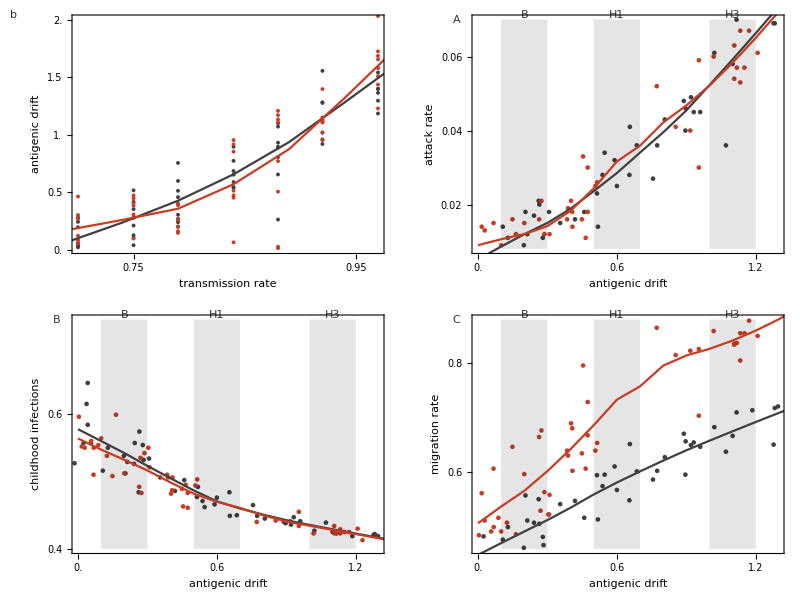

```mathematica
transmissionFig=Grid[Partition[plots,2],Spacings->{1,1}]
```

```mathematica
Export["figures/transmission_results.png",transmissionFig,"PNG",ImageResolution->300]
```

figures/transmission_results.png

```mathematica
Export["figures/transmission_results.pdf",transmissionFig,"PDF"]
```

figures/transmission_results.pdf

## Combined figure

```mathematica
fig=Grid[{{persistenceFig},{transmissionFig}}]
```

-Graphics-
-Graphics-

```mathematica
Export["figures/persistence_transmission.png",fig,"PNG",ImageResolution->300]
```

figures/persistence_transmission.png

```mathematica
Export["figures/persistence_transmission.pdf",fig,"PDF"]
```

figures/persistence_transmission.pdf